```mathematica
l[k_, t_, th_]:=(1/k!)*(2/th^2)^k*Dt[((t-th)t)^k, {t, k}]
```

```mathematica
FullSimplify[l[0, t, th]/.Dt[th,t]->0/.Dt[th,{t, _}]->0]
```

1

```mathematica
FullSimplify[l[1, t, th]/.Dt[th,t]->0/.Dt[th,{t, _}]->0]
```

(4 t-2 th)/th^2

```mathematica
FullSimplify[l[2, t, th]/.Dt[th,t]->0/.Dt[th,{t, _}]->0]
```

(4 (6 t^2-6 t th+th^2))/th^4

```mathematica
FullSimplify[l[3, t, th]/.Dt[th,t]->0/.Dt[th,{t, _}]->0]
```

(8 (2 t-th) (10 t^2-10 t th+th^2))/th^6

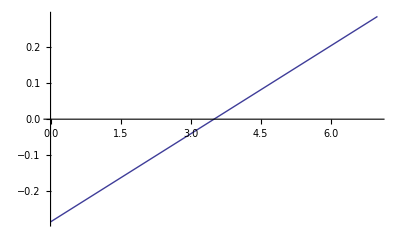

```mathematica
Plot[(4 t-2 th)/th^2/.th->7, {t, 0, 7}]
```